7.94049+0.16598 ⅈ

7.94222

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {0.0001, 0.}.

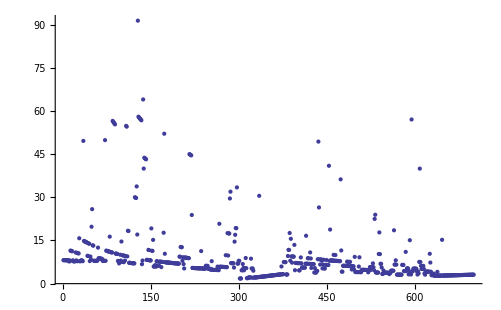

```mathematica
Clear[ω,  sol, w, r, c, fp, ωp, a, γ];
c = 300;
fp =2.183; 
ωp = 2π fp;
a = 20;
r = 100;
γ =6.46*10^(-3);
ϵ[ω_] := 1- ωp^2/(ω^2 + ⅈ γ ω);
α[ω_] := (ϵ[ω] - 1)/(ϵ[ω]+2) a^3; 
f[ω_, r_] := Exp[ⅈ ω r/ c]/r (ω^2/c^2 + (ⅈ ω)/(c r) - 1/r^2);
h[ω_, r_] := 2 Exp[ⅈ ω r/ c]/r (1/r^2 - (ⅈ ω)/(c r));
X = {{0, 0, 0 }, {0, 0, 0 }, {0, 0, α[ω] h[ω, r] }};
MatrixForm[X];
Y = X.X;
MatrixForm[Y];
Det[IdentityMatrix[3] - Y];
sol = FindRoot[Det[IdentityMatrix[3] - Y]==0, {ω, 3}][[1]][[2]]
w = Abs[sol]

Clear[ω, sol, w, r, listY, listX];
listX = {};
listY = {};
Do[r = i;
AppendTo[listX, N[r]];
X = {{α[ω] f[ω, r],0, 0 }, {0,0, 0 }, {0, 0, 0}};
MatrixForm[X];
Y = X.X;
MatrixForm[Y];
Det[IdentityMatrix[3] - Y];
sol = FindRoot[Det[IdentityMatrix[3] - Y]==0, {ω,3}, AccuracyGoal -> Infinity, PrecisionGoal -> 40][[1]][[2]];
w = Abs[sol];
AppendTo[listY, w], {i, 100, 800, 1}]
ListPlot[listY]
```